C:\Users\Matthew\Dropbox\Dissertate-Harvard-LaTeX\figures\ch3

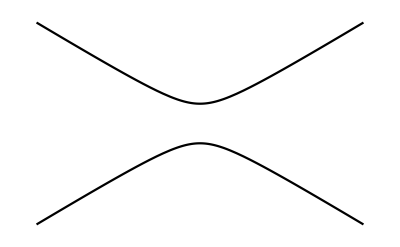

QPT_2eigs.pdf

```mathematica
SetDirectory[NotebookDirectory[]]
Ham[E_]:={{+E,-1},{-1,-E}}
Plot[
{Eigenvalues[Ham[x]]⟦1⟧,
Eigenvalues[Ham[x]]⟦2⟧},{x,-5,5},
PlotStyle-> {Black,Black},
Axes-> None,
Frame-> Automatic,
FrameTicks-> {None,None}
]
Export["QPT_2eigs.pdf",%]
```

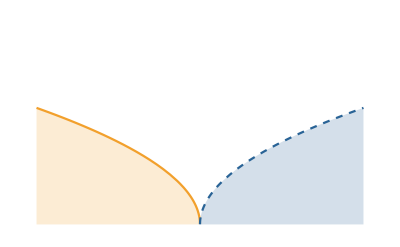

QPT_fan.pdf

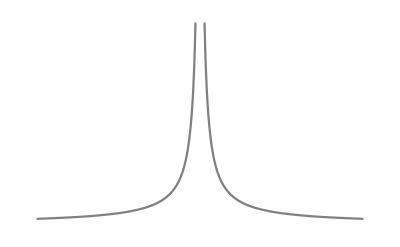

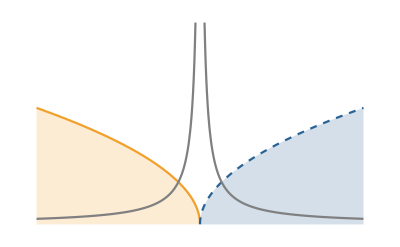

QPT_fan_xi.pdf

```mathematica
P1=Plot[
{√-x,
√x},{x,-3,3},
Filling-> Axis,
PlotRange-> {{-3,3},{0,3}},
PlotStyle-> {{RGBColor[243/256,161/256,44/256]},{RGBColor[41/256,99/256,151/256],Dashed},{Black, Dashed}},
Axes-> None,
Frame-> {Automatic,Automatic,None,None},
FrameTicks-> {None,None}
]
Export["QPT_fan.pdf",%]
P2=Plot[
{Abs[0.25/x]},{x,-3,3},
PlotRange-> {{-3,3},{0,3}},
PlotStyle-> {Gray},
Axes-> None,
Frame-> {Automatic,Automatic,None,None},
FrameTicks-> {None,None}]
Show[P1,P2]
Export["QPT_fan_xi.pdf",%]
```